```mathematica
(*Mathematica Code for Figure 3 in `CV QKD with Single Quadrature Measurement at Arbitrary Reference Frame'*)
```

```mathematica
(*Alice & Bob's Matrix*)
s:=Sin[a]
c:=Cos[a]
M[l_,e_] :={{v,0,x[l]*c,0},{0,v,-x[l]*s,-x[l]},{x[l]*c,-x[l]*s,y[l,e],z[l]*s},{0,-x[l],z[l]*s,y[l,e]}}
P:={{c,0},{0,s}}
Assumptions=x[l],y[l],z[l]>0
Assumptions=True
MatrixForm[M]
```

Syntax::tsntxi: "Assumptions=x[l],y[l],z[l]>0" is incomplete; more input is needed.

```mathematica
det[l_,e_]:=Det[M[l,e]]
```

```mathematica
A1 := {{v,0},{0,v}}
D1 := Det[A1]
```

```mathematica
A2[l_,e_] := {{y[l,e],z[l]*Sin[a]},{z[l]* Sin[a],y[l,e]}}
D2[l_,e_]:=Det[A2[l,e]]
```

```mathematica
A3[l_]:={{x[l]*Cos[a],0},{-x[l]* Sin[a],-x[l]}}
A3T[l_]:=Transpose[A3[l]]
D3[l_]:=Det[A3[l]]
```

```mathematica
(*To find A given B*)
M2[l_,e_]:=P.A2[l,e].P
M3[l_,e_]:=PseudoInverse[M2[l,e]]
M4[l_,e_]:=A3[l].M3[l,e].A3T[l]
M5[l_,e_]:=A1-M4[l,e]
liste[l_,e_]:=FullSimplify[Eigenvalues[M5[l,e]]]
```

```mathematica
Del[l_,e_]:=D1+D2[l,e]+2*D3[l] 
Eig2[l_,e_]:=√((Del[l,e]+√(Del[l,e]^2-4(det[l,e])))/2)
Eig1[l_,e_]:=√((Del[l,e]-√(Del[l,e]^2-4(det[l,e])))/2)
Eig3[l_,e_]:=Part[liste[l,e],1](*√(v(v-(t(v^2-1))/y))*)
f[E_]:=((E+1)/2)Log2[((E+1)/2)]-((E-1)/2)Log2[((E-1)/2)]
f1[l_,e_]:=f[Eig1[l,e]]+f[Eig2[l,e]]
f2[l_,e_]:=f[Eig3[l,e]]
χ[l_,e_]:=(f1[l,e]-f2[l,e])
```

```mathematica
SNR[l_,e_]:= (t[l] * (v-1))/(1+e)
IAB[l_,e_]:=1/2 Log2[1+SNR[l,e]]
```

```mathematica
r[l_,e_]:=be*IAB[l,e] -χ[l,e]
r2[l_,e_]:= (5*10^6)*r[l,e]
```

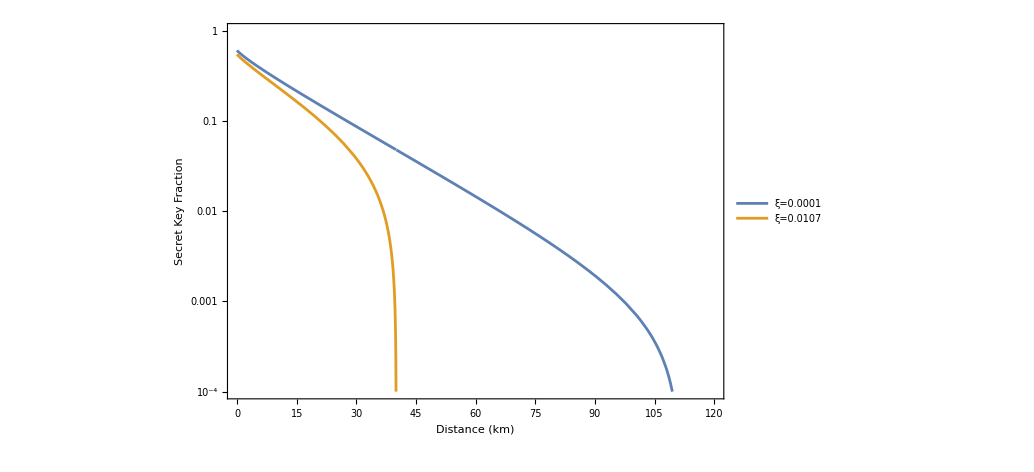

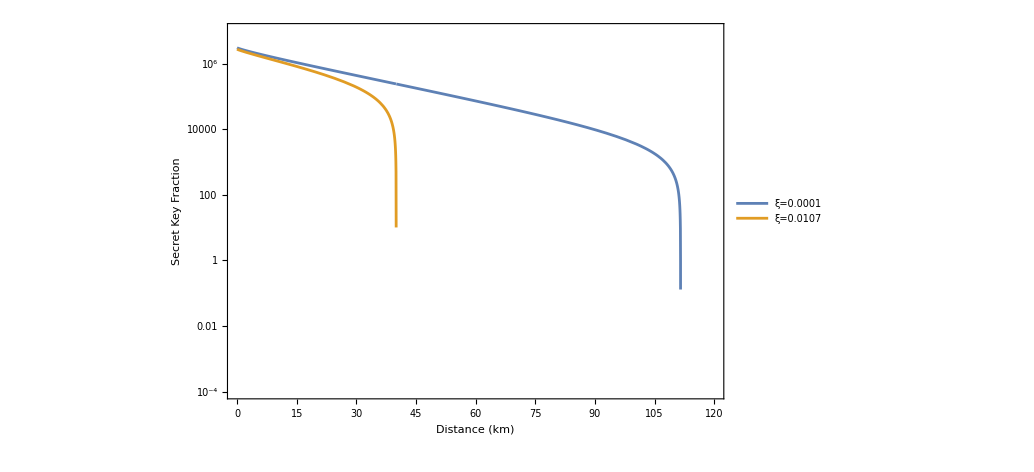

```mathematica
a:=0
be:=0.95
x[l_]:=√(t[l]*(v^2-1))
y[l_,e_]:=(t[l]*(v-1)+1+e)
z[l_]:=(t[l]*(v+1))/2
v:=1.2
t[l_]:=10^(-0.025*l)
list:=List[0.0001,0.0107]
LogPlot[Evaluate[Table[r[l,e],{e,list}]],{l,0,120},PlotRange->{{0,120},{0.0001,1}},Frame->True,FrameLabel->{{HoldForm["Secret Key Fraction"],None},{HoldForm["Distance (km)"],None}},LabelStyle->{Directive[Black,24]},PlotLegends->Placed[{"ξ=0.0001","ξ=0.0107"},{Right,Top}]]
LogPlot[Evaluate[Table[r2[l,e],{e,list}]],{l,0,120},PlotRange->{{0,120},{0.0001,10^7}},Frame->True,FrameLabel->{{HoldForm["Secret Key Fraction"],None},{HoldForm["Distance (km)"],None}},LabelStyle->{Directive[Black,24]},PlotLegends->Placed[{"ξ=0.0001","ξ=0.0107"},{Right,Top}]]
(*Plot[{t[l]},{l,0,120},PlotStyle->{Blue},PlotRange->{{0,120},{}}]*)
(*plot1:=Block[{e=0.0001},LogPlot[{t[l]},{l,0,120},PlotStyle->{Blue},PlotRange->{{0,120},{0.0001,1}}]]*)
(*plot2:=Block[{e=0.0107},LogPlot[{r[l]},{l,0,120},PlotStyle->{Black},PlotRange->{{0,120},{0.0001,1}}]]*)
(*plot=Show[plot1,plot2,AxesLabel->{Style["Distance (km)",Bold,12],Style["Secret Key Fraction",Bold,12]},Axes->True]*)
(*plot=Show[plot1,plot2,FrameLabel->{{HoldForm[Secret Key Fraction],None},{HoldForm[Distance -km],None}},Frame->True,LabelStyle->{Directive[Black,12]}]*)
(*ShowLegend[plot,{{{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ξ=0.0001"},{Graphics[{Black,Line[{{0,0},{2,0}}]}],"ξ=0.0107"}},LegendPosition->{0.62,0.35},LegendSize->{0.25,0.2},LegendShadow->False,LegendMarkerSize->20}]*)
```

```mathematica
s
```

0